# Random graphs with games

## Parameters

```mathematica
p=0.7;n=100;θ=1/(p n);
```

```mathematica
1./(p n)
```

0.0142857

## Variables, Functions, Measures

```mathematica
(* conditional degree *)
K[g_,i_,l_]:=VertexDegree[g,l]AdjacencyMatrix[g]⟦i,l⟧
(* normalization factor for the conditional degree *)
λ[g_,i_]:=Plus@@(K[g,i,#]&/@Range[n])
μ[g_,i_]:=Plus@@(Replace[Quiet[(1./K[graph,1,#])&/@Range[n]],q_?(!NumberQ@#&):>0,{1}])
(* normalized conditional degree *)
w[g_,i_,j_]:=With[{l=λ[g,i]},If[l>0,K[g,i,j]/N@l,0.]]
w[g_,i_]:=With[{l=λ[g,i]},If[l>0,(K[g,i,#]&/@Range[n])/N@l,0.]]
ncdMatrix[g_]:=w[g,#]&/@Range[n]
(* inverse normalized conditional degree *)
ζ[g_,i_,j_]:=With[{m=μ[g,i]},If[m>0,(1/K[g,i,j])/N@m,0.]]
ζ[g_,i_]:=With[{m=μ[g,i]},If[m>0,((1/K[g,i,#])&/@Range[n])/N@m,0.]]
incdMatrix[g_]:=ζ[g,#]&/@Range[n]
```

## Procedures

### Create a new graph

```mathematica
newgraph[]:=RandomGraph[BernoulliGraphDistribution[n,p],DirectedEdges->False];
newgraph[num_]:=RandomGraph[BernoulliGraphDistribution[n,p],num,DirectedEdges->False]
```

### Delete edges with weakest signals at each step

```mathematica
(*weakest[]:=
Module[{newgraph=graph},
Do[newgraph⟦i,j⟧=0;newgraph⟦j,i⟧=0,{i,1,n},{j,minids[i]}];
graph= newgraph;]*)
```

### Delete edges with signals below threshold

```mathematica
threshold[g_]:=
Module[{m},
(* m_ij will be 0 if the edge i->j should be deleted. This happens when either w_ij or w_ji is below θ. For this, we multiply the matrix by its transpose *)
m=ncdMatrix[g]/.c_?NumberQ:>If[c<θ,0,1];
m=m*Transpose@m;
AdjacencyGraph@Normal@m]
```

## Play

```mathematica
graph=newgraph[];
g=threshold[graph];
(*Grid[Transpose@{
{"θ","Clustering Coefficient","Characteristic Path Length","Small World"},
With[{subg=Subgraph[g,ConnectedComponents[g]⟦1⟧]},
With[{
crand=GlobalClusteringCoefficient[graph],
cth=GlobalClusteringCoefficient[subg],
lrand=Plus@@Flatten@GraphDistanceMatrix[graph]/(n(n-1))//N,
lth=Plus@@Flatten@GraphDistanceMatrix[subg]/(VertexCount[subg](VertexCount[subg]-1))
},
{
{θ,Mean@Select[Flatten[ncdMatrix[graph]],#>0.&]},
{crand,cth}//N,
{lrand,lth}//N,
{crand/lrand,cth/lth}//N
}]]}]*)
```

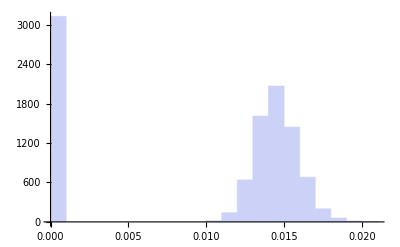

```mathematica
Histogram[Flatten@ncdMatrix[graph]]
```

```mathematica
EdgeCount/@{graph,g}
```

{3436,437}

```mathematica
Grid[{{graph,g}}]
```

-Graphics- | -Graphics-

## Stats

```mathematica
{crand,lrand}=Transpose@RandomVariate[GraphPropertyDistribution[{GlobalClusteringCoefficient[gr],Plus@@Flatten@GraphDistanceMatrix[gr]/(n(n-1))},gr\[Distributed]BernoulliGraphDistribution[n,p]],500]//N;//AbsoluteTiming
```

{1.39236,Null}

```mathematica
swth=
Table[
graph=newgraph[];
gth=threshold[graph];
subg=Subgraph[gth,ConnectedComponents[gth]⟦1⟧];
With[{ns=VertexCount[subg]},
(GlobalClusteringCoefficient[subg]/Mean@crand)/((Plus@@Flatten@GraphDistanceMatrix[subg]/(ns(ns-1)))/Mean@lrand)
],
{500}]//N;//AbsoluteTiming
```

{647.10293,Null}

```mathematica
Mean@swth
```

0.863051